# 2. izpit – Mathematica

## Računalniški praktikum 2024/25

Študijska smer : Aplikativna matematika in Aplikativna fizika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

V tem delu izpita sta dve nalogi, ki sta skupaj vredni 32 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.

## 1. naloga [10 točk]

1. (5 točk)  Izračunajte prvi odvod funkcije ln(sin(e^(2x))) in ga poenostavite.
2. (5 točk) Numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
D[Log[Sin[Exp[2 x]]],x]
FindRoot[Cos[x]/(Exp[x^3-1]),{x,1}]
```

2 ⅇ^(2 x) Cot[ⅇ^(2 x)]

{x→1.5708}

## 2. naloga [22 točk]

Naj bo dana funkcija f(n)=1/(9 n^2+15 n+4).
1. (5 točk) Definirajte funkcijo f  in izračunajte f(2025).
2. (6 točk) S pomočjo funkcije DiscretePlot narišite točkovni graf f(n) za naravna števila 1≤n≤50.
3. (6 točk) Definirajte funkcijo g kot vsoto g(m) = f(m)+f(m+1)+…+f(2025m).
4. (5 točk) Izračunajte limito lim_(m→∞) g(m).

1/36936004

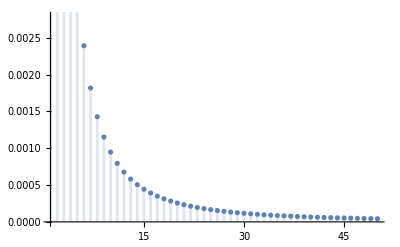

```mathematica
f[n_]:=1/(9n^2+15n+4)
f[2025]
DiscretePlot[f[n],{n,1,50}]
g[m_]:=Sum[f[i],{i,m,2025m}]
Limit[g[m],m->Infinity];
```